## Numerical plot for α,β

```mathematica
α=0.3;
β=0.6;
i[n_?NumericQ,τ_?NumericQ]:=NIntegrate[x^(β-1)/(1+x)^(α+β)E^(-2(n+1)^2(1+x)^2/τ),{x,0,∞},Method->"GlobalAdaptive"];
g[τ_?NumericQ]:=(2(α-1))/((α+1)Beta[α,β])NSum[Pochhammer[(3-α)/2,n]/Pochhammer[(3+α)/2,n] i[n,τ],{n,0,IntegerPart[√τ]},Method->"WynnEpsilon"];
```

```mathematica
τ=1000.
β √(2/(π τ))(1-g[τ])
Clear[τ]
```

1000.

0.0762869

```mathematica
tableg=Table[{τ,β √(2/(π τ))(1-g[τ])}/.τ->10^k,{k,-4.,5.,0.05}];
tabletauexp=Table[tableg[[i]][[1]],{i,1,Length[tableg]}];
tablegexp=Table[tableg[[i]][[2]],{i,1,Length[tableg]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

```mathematica
Export[StringTemplate["C:\\Users\\julie\\Nextcloud\\These\\Data\\records\\records\\Data\\s-phi``.csv"][ϕ],tablegexp]
Export[StringTemplate["C:\\Users\\julie\\Nextcloud\\These\\Data\\records\\records\\Data\\tau-phi``.csv"][ϕ],tabletauexp]
```

C:\Users\julie\Nextcloud\These\Data\records\records\Data\s-phi0.367879.csv

C:\Users\julie\Nextcloud\These\Data\records\records\Data\tau-phi0.367879.csv

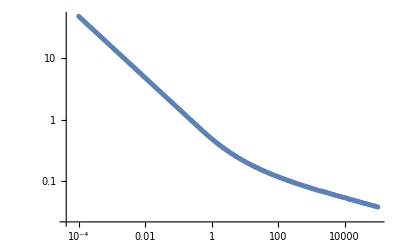

```mathematica
ListLogLogPlot[tableg,PlotRange->All]
```

## Numerical tests of integral equalities

```mathematica
ϕ=3/4;
μ=0.000000000001;
k=1;
(*NIntegrate[m^(ϕ-1)/(1+m)^(2ϕ)Coth[(1+m)μ],{m,0,∞}];
(*μ ϕ NIntegrate[m1^(ϕ-1)/(1+m1)^(2ϕ)Sinh[μ(1+m1)]^(ϕ-1)/Sinh[μ(1+m2)]^(ϕ+1),{m1,0,∞},{m2,m1,∞},Method->"LocalAdaptive"]*)
2 ϕ/(1+ϕ) NIntegrate[m^(ϕ-1)/(1+m)^(2ϕ)(Coth[(1+m)μ]-1)Hypergeometric2F1[(1-ϕ)/2,1,(3+ϕ)/2,E^(-2(1+m)μ)],{m,0,∞},Method->"GlobalAdaptive"];
%/%%;*)
μ/Beta[ϕ,ϕ] NIntegrate[m^(ϕ-1)/(1+m)^(2ϕ)Coth[(1+m)μ]-2 ϕ/(1+ϕ)m^(ϕ-1)/(1+m)^(2ϕ)(Coth[(1+m)μ]-1)Hypergeometric2F1[(1-ϕ)/2,1,(3+ϕ)/2,E^(-2(1+m)μ)],{m,0,∞}]

μ/Beta[ϕ,ϕ] NIntegrate[m^(ϕ-1)/(1+m)^(2ϕ)(Coth[(1+m)μ](1-2 ϕ/(1+ϕ)Hypergeometric2F1[(1-ϕ)/2,1,(3+ϕ)/2,E^(-2(1+m)μ)])+2 ϕ/(1+ϕ)Hypergeometric2F1[(1-ϕ)/2,1,(3+ϕ)/2,E^(-2(1+m)μ)]),{m,0,∞},Method->"GlobalAdaptive"]
μ(1-1/Beta[ϕ,ϕ] NIntegrate[m^(ϕ-1)/(1+m)^(2ϕ)E^(-μ(1+m))/Sinh[μ(1+m)](2 ϕ/(1+ϕ)Hypergeometric2F1[(1-ϕ)/2,1,(3+ϕ)/2,E^(-2(1+m)μ)]-1),{m,0,∞},Method->"GlobalAdaptive"])
μ(1-(2(ϕ-1))/(Beta[ϕ,ϕ](ϕ+1))NIntegrate[m^(ϕ-1)/(1+m)^(2ϕ)E^(-2μ(1+m))(Hypergeometric2F1[(3-ϕ)/2,1,(3+ϕ)/2,E^(-2(1+m)μ)]),{m,0,∞},Method->"GlobalAdaptive"])
```

6.93962×10^-10

6.93962×10^-10

6.93962×10^-10

6.93961×10^-10